```mathematica
(* Load package *)
(* If the Needs command fails just open CrosswordCounts.nb or CrosswordCounts.m and run the code *)
Needs["CrosswordCounts`"]
```

```mathematica
(* List functions available in package *)
?CrosswordCounts`*
```

```mathematica
(* The workhorse function in the package is "count".  This counts the number of "valid" crossword puzzle grids, as defined in the January 18, 2019 edition of The Riddler at fivethirtyeight.com. *)
?count
```

count[m,n,w,t] returns the number of symmetric, connected m × n grids with words of length ≥ w (called "valid" grids).
	If t == 1 the grids must be tight (white squares touch each border wall) and if t == 0 the grids can be loose.
	count[m,n,w,t] == count[n,m,w,t] though it is more efficient to put the larger of m and n as the first argument.
count[n,w,t] may be used for the square case (number of valid n × n grids).
Options:
	compMode:  Computation mode.
		≤ 0 to output single count (0 = silent, -1 = verbose),
		> 0 to output list of counts (1 = silent, 2 = print results as computed, 3 = verbose)
		Default:  0
	readIndex:  1 to start from scratch, ≥ 2 to read corresponding save file
		Default:  1
	saveQ:  Whether to save intermediate results
		Default:  False
	saveRoot:  Root of save file name for reading (readIndex ≥ 2) and  writing (saveQ == True)
		Default:  "cws"
	saveDirectory:  Directory for save files
		Default:  Automatic (= directory of notebook calling the package)

```mathematica
(* Here we count the number of 6 x 6 grids with words of minimum length 2.  The third argument, 1, indicates we are requiring the grids to be "tight":  i.e., to have white squares touching all four walls so that there are no extraneous black borders -- this was not explicitly required in The Riddler's problem statement, but we will treat this as the standard case. *)
count[6,2,1]
```

484

```mathematica
(* We can check that this count is correct by explicitly enumerating all valid, tight grids.  These grids come in five symmetry classes, depending on which operations map a grid to itself.  When we include only one member from each symmetry class, we reduce the 484 grids to 152. There are 8, 7, 38, 5, and 94 grids in each symmetry class, respectively.  *)
nValidGrids[6,2,1]
nValidGridClasses[6,2,1]
sizeList=sizesValidGridClasses[6,2,1]
sizeList.{1,2,2,2,4}
```

484

152

{8,7,38,5,94}

484

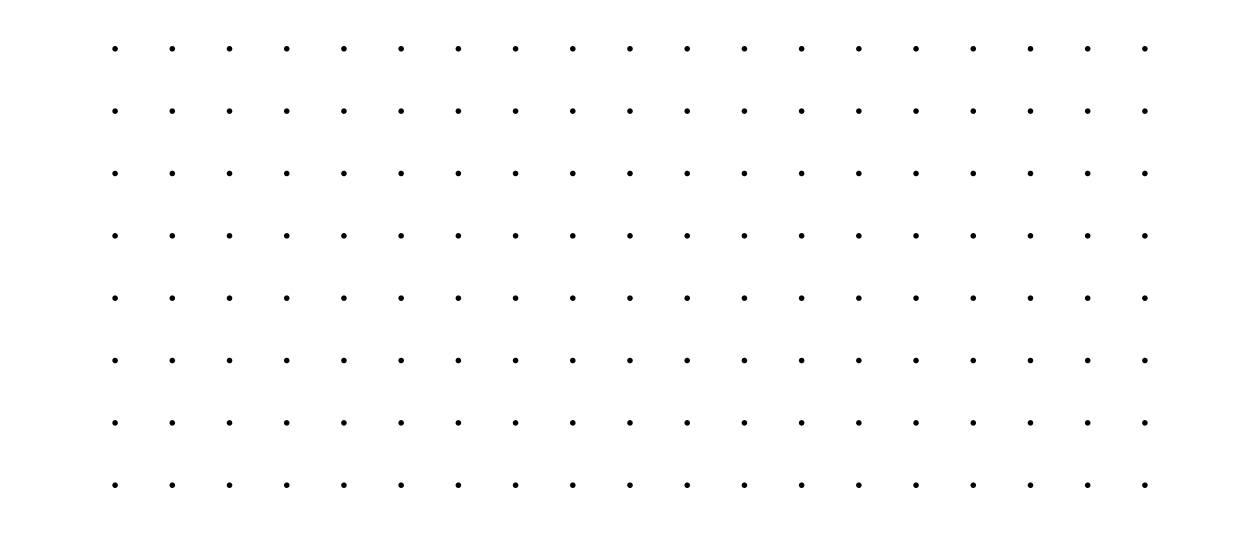

```mathematica
(* We now plot these 152 grids, color-coded by symmetry class *)
plotGrids[allValidGridClasses[6,2,1],10]
```

```mathematica
(* Most of these grids are not "maximal" -- these are essentially grids with no extraneous black squares. We plot the 11 of these that are maximal. *)
plotGrids[allMaximalGridClasses[6,2],10,20]
```

-Graphics-

```mathematica
(* The routines that explicitly construct grids do not scale to the 15 x 15 case (with minimum word length w = 3) from The Riddler.  The "count" routine uses a more sophisticated dynamic programming method that (barely) scales to problems this large.  Results of running count are stored in the CrosswordCounts package.  One function that encodes these is tightSquareCount, which stores results of count[n,w,1] for n = 1 to 15 and w = 1 to 7, along with formulas for simple patterns that emerge (these formulas fill in the entire w = 8 row below). The -1 entries are unknown values. *)
Table[tightSquareCount[n,w],{w,8},{n,16}]//MatrixForm
```

(1 | 1 | 11 | 47 | 1411 | 21411 | 2123851 | 124511195 | 42999348087 | 9581445219371 | 11829924769055787 | -1 | -1 | -1 | -1 | -1
0 | 1 | 3 | 10 | 59 | 484 | 7250 | 181575 | 6826137 | 446562953 | 43131669850 | 7112223095914 | -1 | -1 | -1 | -1
0 | 0 | 1 | 3 | 12 | 48 | 312 | 2190 | 31187 | 586731 | 17438702 | 654057540 | 40575832476 | 3115321983734 | 404139015237875 | -1
0 | 0 | 0 | 1 | 3 | 12 | 50 | 208 | 1336 | 9119 | 113415 | 1993875 | 37724992 | 1290193576 | 45949047420 | -1
0 | 0 | 0 | 0 | 1 | 3 | 12 | 50 | 210 | 880 | 5971 | 38421 | 487427 | 7583483 | 126501143 | -1
0 | 0 | 0 | 0 | 0 | 1 | 3 | 12 | 50 | 210 | 882 | 3694 | 25455 | 165436 | 2079601 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 3 | 12 | 50 | 210 | 882 | 3696 | 15442 | 109248 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 3 | 12 | 50 | 210 | 882 | 3696 | 15444 | 64348)

```mathematica
(* The other stored results are encoded in countMat15[3,1], which could be computed directly (over several days) as countMat[15,3,1].  This gives the number of m x n grids with minimum word length 3 for the tight case (t = 1).  From this matrix we can easily determine that analogous loose result countMat15[3,0].  *)
countMat15[3,1]//MatrixForm
countMat15[3,0]//MatrixForm
(* We take the last element of each matrix to get the answer to The Riddler's puzzle for the tight and loose cases, respectively. Each of these is slightly over 400 trillion (so too large to count directly) *)
answer538 = {countMat15[3,1][[15,15]],countMat15[3,0][[15,15]]}
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 1 | 3 | 5 | 7 | 7 | 13 | 15 | 33 | 37 | 75 | 89 | 175 | 211
0 | 0 | 1 | 5 | 12 | 22 | 34 | 64 | 115 | 259 | 468 | 980 | 1742 | 3606 | 6519
0 | 0 | 1 | 7 | 22 | 48 | 86 | 178 | 367 | 973 | 2132 | 5456 | 11520 | 28508 | 60985
0 | 0 | 1 | 7 | 34 | 86 | 312 | 626 | 1754 | 3990 | 12931 | 30741 | 100126 | 234362 | 749439
0 | 0 | 1 | 13 | 64 | 178 | 626 | 2190 | 6746 | 21972 | 66411 | 234143 | 738990 | 2613144 | 8061187
0 | 0 | 1 | 15 | 115 | 367 | 1754 | 6746 | 31187 | 108089 | 472654 | 1599558 | 7463594 | 25710394 | 119869867
0 | 0 | 1 | 33 | 259 | 973 | 3990 | 21972 | 108089 | 586731 | 2542446 | 13038460 | 57394116 | 298289312 | 1325038289
0 | 0 | 1 | 37 | 468 | 2132 | 12931 | 66411 | 472654 | 2542446 | 17438702 | 85912738 | 571540158 | 2794999844 | 18851755888
0 | 0 | 1 | 75 | 980 | 5456 | 30741 | 234143 | 1599558 | 13038460 | 85912738 | 654057540 | 4163555192 | 30763310300 | 196071884168
0 | 0 | 1 | 89 | 1742 | 11520 | 100126 | 738990 | 7463594 | 57394116 | 571540158 | 4163555192 | 40575832476 | 287957992192 | 2772709489316
0 | 0 | 1 | 175 | 3606 | 28508 | 234362 | 2613144 | 25710394 | 298289312 | 2794999844 | 30763310300 | 287957992192 | 3115321983734 | 28813678808484
0 | 0 | 1 | 211 | 6519 | 60985 | 749439 | 8061187 | 119869867 | 1325038289 | 18851755888 | 196071884168 | 2772709489316 | 28813678808484 | 404139015237875)

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8
1 | 1 | 2 | 4 | 7 | 11 | 14 | 24 | 29 | 57 | 66 | 132 | 155 | 307 | 366
1 | 1 | 3 | 7 | 16 | 30 | 51 | 95 | 167 | 355 | 636 | 1336 | 2379 | 4943 | 8899
1 | 1 | 3 | 11 | 30 | 66 | 123 | 257 | 505 | 1263 | 2674 | 6794 | 14283 | 35477 | 75479
1 | 1 | 4 | 14 | 51 | 123 | 398 | 814 | 2268 | 5064 | 15668 | 36786 | 117537 | 274755 | 873496
1 | 1 | 4 | 24 | 95 | 257 | 814 | 2638 | 7942 | 25616 | 76522 | 265290 | 827121 | 2907117 | 8949504
1 | 1 | 5 | 29 | 167 | 505 | 2268 | 7942 | 35325 | 120281 | 521379 | 1751561 | 8086842 | 27699924 | 128712668
1 | 1 | 5 | 57 | 355 | 1263 | 5064 | 25616 | 120281 | 635325 | 2731307 | 13913459 | 60876022 | 314844598 | 1394036694
1 | 1 | 6 | 66 | 636 | 2674 | 15668 | 76522 | 521379 | 2731307 | 18446135 | 90275325 | 597551756 | 2911223532 | 19569933470
1 | 1 | 6 | 132 | 1336 | 6794 | 36786 | 265290 | 1751561 | 13913459 | 90275325 | 681249133 | 4311975232 | 31745490572 | 201717020072
1 | 1 | 7 | 155 | 2379 | 14283 | 117537 | 827121 | 8086842 | 60876022 | 597551756 | 4311975232 | 41752489853 | 295090915631 | 2833434360883
1 | 1 | 7 | 307 | 4943 | 35477 | 274755 | 2907117 | 27699924 | 314844598 | 2911223532 | 31745490572 | 295090915631 | 3178131715745 | 29306174768955
1 | 1 | 8 | 366 | 8899 | 75479 | 873496 | 8949504 | 128712668 | 1394036694 | 19569933470 | 201717020072 | 2833434360883 | 29306174768955 | 409764131469788)

{404139015237875,409764131469788}

```mathematica
(* We can use countMat to compute results like the above in a reasonable time for small cases.  Here are results for grids up through 6 x 10 with minimum word length w = 2 *)
countMat[6,10,2,1]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 3 | 5 | 5 | 11 | 13 | 29 | 35 | 75
0 | 1 | 5 | 10 | 21 | 36 | 94 | 162 | 423 | 721
0 | 1 | 5 | 21 | 59 | 151 | 349 | 1099 | 2425 | 7897
0 | 1 | 11 | 36 | 151 | 484 | 1790 | 5481 | 20999 | 64138)

```mathematica
(* Here we redo the count[6,2,1] computation with some additional options. We specify compMode -> -1 for verbose output and saveQ -> True to save intermediate results. *)
count[6,2,1,compMode->-1,saveQ->True]
```

Δt = 0.001: Row 1/3 complete - 12 states, partial count = 20

Δt = 0.022001: Row 2/3 complete - 54 states, partial count = 100

Δt = 0.0760043: Row 3/3 complete - 105 states, partial count = 952

Δt = 0.0090006: Final step

484

```mathematica
(* The "count" function builds up partial results one row at a time:  the files "cws_T2_6_2.wl" and "cws_T2_6_3.wl" output by the above command store intermediate states of the computation after row 2 and row 3.  Looking at "cws_T2_6_3.wl" provides an indication of how "count" works. This file contain a list of 105 possible "states" of the third row and an associated count for each.  One entry in this list is {{1, 1, 2, 0, 2, 2}, {1, 1}, True} -> 10.  The {1, 1, 2, 0, 2, 2} indicates a row with 5 white squares (positive numbers) and one black one (the 0).  The positive numbers range from 1 to w, indicating the length of the current vertical run of white squares in each column. This is important to track because positive numbers < w cannot continue with a 0, lest they have a word of length < w.  The second component of the state we're looking at is {1, 1}.  This list has length 2 because there are two runs of white squares in the current row.  The {1, 1} are "labels" for these runs.  The fact that the labels are the same specifies that these two runs are connected somewhere in a previous row:  both are part of "cluster 1".  Finally, the "True" indicates that the requirement of touching both side walls has been met.  The total number of 6 x 3 grids that achieve this state in their third row is 10.  Given all this information, we can then determine the total number of valid 6 x 6 grids that can be formed by matching these partial states to themselves (when rotated by 180°). *)

(* We can also read the state in and evolve it two more rows to count the number of 10 x 6 grids, which must agree with the 6 x 10 entry in countMat[6,10,2,1] above *)
count[10,6,2,1,compMode->-1,readIndex->3]
```

Δt = 0.012001: Row 3/5 read - 105 states, partial count = 952

Δt = 0.122007: Row 4/5 complete - 110 states, partial count = 11675

Δt = 0.126007: Row 5/5 complete - 110 states, partial count = 138343

Δt = 0.0070004: Final step

64138

```mathematica
(* When computing the desired result count[15,3,1] the 7th and final-row stage of the computation had 5,967,789 states encompassing a total of 209,631,035,845,190 partial grids.  This large number of partial grids per state is what enabled the algorithm to enumerate all 400 trillion+ grids.  However, this dynamic programming approach is harder to verify that direct computation.  Therefore, the a number of consistency routines are required to check that the numbers being produced by "count" agree with those produced by direct enumeration. *)
checkAllQ[]
```

allSymGrids[1,1] equals the symmetric grids in allGrids[1,1]? True

allSymGrids[1,2] equals the symmetric grids in allGrids[1,2]? True

allSymGrids[2,1] equals the symmetric grids in allGrids[2,1]? True

allSymGrids[1,3] equals the symmetric grids in allGrids[1,3]? True

allSymGrids[3,1] equals the symmetric grids in allGrids[3,1]? True

allSymGrids[1,4] equals the symmetric grids in allGrids[1,4]? True

allSymGrids[2,2] equals the symmetric grids in allGrids[2,2]? True

allSymGrids[4,1] equals the symmetric grids in allGrids[4,1]? True

allSymGrids[1,5] equals the symmetric grids in allGrids[1,5]? True

allSymGrids[5,1] equals the symmetric grids in allGrids[5,1]? True

allSymGrids[1,6] equals the symmetric grids in allGrids[1,6]? True

allSymGrids[2,3] equals the symmetric grids in allGrids[2,3]? True

allSymGrids[3,2] equals the symmetric grids in allGrids[3,2]? True

allSymGrids[6,1] equals the symmetric grids in allGrids[6,1]? True

allSymGrids[1,7] equals the symmetric grids in allGrids[1,7]? True

allSymGrids[7,1] equals the symmetric grids in allGrids[7,1]? True

allSymGrids[1,8] equals the symmetric grids in allGrids[1,8]? True

allSymGrids[2,4] equals the symmetric grids in allGrids[2,4]? True

allSymGrids[4,2] equals the symmetric grids in allGrids[4,2]? True

allSymGrids[8,1] equals the symmetric grids in allGrids[8,1]? True

allSymGrids[1,9] equals the symmetric grids in allGrids[1,9]? True

allSymGrids[3,3] equals the symmetric grids in allGrids[3,3]? True

allSymGrids[9,1] equals the symmetric grids in allGrids[9,1]? True

allSymGrids[1,10] equals the symmetric grids in allGrids[1,10]? True

allSymGrids[2,5] equals the symmetric grids in allGrids[2,5]? True

allSymGrids[5,2] equals the symmetric grids in allGrids[5,2]? True

allSymGrids[10,1] equals the symmetric grids in allGrids[10,1]? True

allWrdGrids[2,2,2] equals the grids in allGrids[2,2] with words of length ≥ 2? True

allWrdGrids[2,3,2] equals the grids in allGrids[2,3] with words of length ≥ 2? True

allWrdGrids[3,2,2] equals the grids in allGrids[3,2] with words of length ≥ 2? True

allWrdGrids[2,4,2] equals the grids in allGrids[2,4] with words of length ≥ 2? True

allWrdGrids[4,2,2] equals the grids in allGrids[4,2] with words of length ≥ 2? True

allWrdGrids[3,3,2] equals the grids in allGrids[3,3] with words of length ≥ 2? True

allWrdGrids[3,3,3] equals the grids in allGrids[3,3] with words of length ≥ 3? True

allWrdGrids[2,5,2] equals the grids in allGrids[2,5] with words of length ≥ 2? True

allWrdGrids[5,2,2] equals the grids in allGrids[5,2] with words of length ≥ 2? True

allSymWrdGrids[2,2,2] equals the symmetric grids in allWrdGrids[2,2,2]? True

allSymWrdGrids[2,2,2] equals the grids in allSymGrids[2,2] with words of length ≥ 2? True

allSymWrdGrids[2,3,2] equals the symmetric grids in allWrdGrids[2,3,2]? True

allSymWrdGrids[2,3,2] equals the grids in allSymGrids[2,3] with words of length ≥ 2? True

allSymWrdGrids[3,2,2] equals the symmetric grids in allWrdGrids[3,2,2]? True

allSymWrdGrids[3,2,2] equals the grids in allSymGrids[3,2] with words of length ≥ 2? True

allSymWrdGrids[2,4,2] equals the symmetric grids in allWrdGrids[2,4,2]? True

allSymWrdGrids[2,4,2] equals the grids in allSymGrids[2,4] with words of length ≥ 2? True

allSymWrdGrids[4,2,2] equals the symmetric grids in allWrdGrids[4,2,2]? True

allSymWrdGrids[4,2,2] equals the grids in allSymGrids[4,2] with words of length ≥ 2? True

allSymWrdGrids[3,3,2] equals the symmetric grids in allWrdGrids[3,3,2]? True

allSymWrdGrids[3,3,2] equals the grids in allSymGrids[3,3] with words of length ≥ 2? True

allSymWrdGrids[3,3,3] equals the symmetric grids in allWrdGrids[3,3,3]? True

allSymWrdGrids[3,3,3] equals the grids in allSymGrids[3,3] with words of length ≥ 3? True

allSymWrdGrids[2,5,2] equals the symmetric grids in allWrdGrids[2,5,2]? True

allSymWrdGrids[2,5,2] equals the grids in allSymGrids[2,5] with words of length ≥ 2? True

allSymWrdGrids[5,2,2] equals the symmetric grids in allWrdGrids[5,2,2]? True

allSymWrdGrids[5,2,2] equals the grids in allSymGrids[5,2] with words of length ≥ 2? True

allSymWrdGrids[2,6,2] equals the symmetric grids in allWrdGrids[2,6,2]? True

allSymWrdGrids[2,6,2] equals the grids in allSymGrids[2,6] with words of length ≥ 2? True

allSymWrdGrids[3,4,2] equals the symmetric grids in allWrdGrids[3,4,2]? True

allSymWrdGrids[3,4,2] equals the grids in allSymGrids[3,4] with words of length ≥ 2? True

allSymWrdGrids[4,3,2] equals the symmetric grids in allWrdGrids[4,3,2]? True

allSymWrdGrids[4,3,2] equals the grids in allSymGrids[4,3] with words of length ≥ 2? True

allSymWrdGrids[6,2,2] equals the symmetric grids in allWrdGrids[6,2,2]? True

allSymWrdGrids[6,2,2] equals the grids in allSymGrids[6,2] with words of length ≥ 2? True

allSymWrdGrids[3,4,3] equals the symmetric grids in allWrdGrids[3,4,3]? True

allSymWrdGrids[3,4,3] equals the grids in allSymGrids[3,4] with words of length ≥ 3? True

allSymWrdGrids[4,3,3] equals the symmetric grids in allWrdGrids[4,3,3]? True

allSymWrdGrids[4,3,3] equals the grids in allSymGrids[4,3] with words of length ≥ 3? True

allSymWrdGrids[2,7,2] equals the symmetric grids in allWrdGrids[2,7,2]? True

allSymWrdGrids[2,7,2] equals the grids in allSymGrids[2,7] with words of length ≥ 2? True

allSymWrdGrids[7,2,2] equals the symmetric grids in allWrdGrids[7,2,2]? True

allSymWrdGrids[7,2,2] equals the grids in allSymGrids[7,2] with words of length ≥ 2? True

allSymWrdGrids[3,5,2] equals the symmetric grids in allWrdGrids[3,5,2]? True

allSymWrdGrids[3,5,2] equals the grids in allSymGrids[3,5] with words of length ≥ 2? True

allSymWrdGrids[5,3,2] equals the symmetric grids in allWrdGrids[5,3,2]? True

allSymWrdGrids[5,3,2] equals the grids in allSymGrids[5,3] with words of length ≥ 2? True

allSymWrdGrids[3,5,3] equals the symmetric grids in allWrdGrids[3,5,3]? True

allSymWrdGrids[3,5,3] equals the grids in allSymGrids[3,5] with words of length ≥ 3? True

allSymWrdGrids[5,3,3] equals the symmetric grids in allWrdGrids[5,3,3]? True

allSymWrdGrids[5,3,3] equals the grids in allSymGrids[5,3] with words of length ≥ 3? True

allSymWrdGrids[2,8,2] equals the symmetric grids in allWrdGrids[2,8,2]? True

allSymWrdGrids[2,8,2] equals the grids in allSymGrids[2,8] with words of length ≥ 2? True

allSymWrdGrids[4,4,2] equals the symmetric grids in allWrdGrids[4,4,2]? True

allSymWrdGrids[4,4,2] equals the grids in allSymGrids[4,4] with words of length ≥ 2? True

allSymWrdGrids[8,2,2] equals the symmetric grids in allWrdGrids[8,2,2]? True

allSymWrdGrids[8,2,2] equals the grids in allSymGrids[8,2] with words of length ≥ 2? True

allSymWrdGrids[4,4,3] equals the symmetric grids in allWrdGrids[4,4,3]? True

allSymWrdGrids[4,4,3] equals the grids in allSymGrids[4,4] with words of length ≥ 3? True

allSymWrdGrids[4,4,4] equals the symmetric grids in allWrdGrids[4,4,4]? True

allSymWrdGrids[4,4,4] equals the grids in allSymGrids[4,4] with words of length ≥ 4? True

allSymWrdGrids[2,9,2] equals the symmetric grids in allWrdGrids[2,9,2]? True

allSymWrdGrids[2,9,2] equals the grids in allSymGrids[2,9] with words of length ≥ 2? True

allSymWrdGrids[3,6,2] equals the symmetric grids in allWrdGrids[3,6,2]? True

allSymWrdGrids[3,6,2] equals the grids in allSymGrids[3,6] with words of length ≥ 2? True

allSymWrdGrids[6,3,2] equals the symmetric grids in allWrdGrids[6,3,2]? True

allSymWrdGrids[6,3,2] equals the grids in allSymGrids[6,3] with words of length ≥ 2? True

allSymWrdGrids[9,2,2] equals the symmetric grids in allWrdGrids[9,2,2]? True

allSymWrdGrids[9,2,2] equals the grids in allSymGrids[9,2] with words of length ≥ 2? True

allSymWrdGrids[3,6,3] equals the symmetric grids in allWrdGrids[3,6,3]? True

allSymWrdGrids[3,6,3] equals the grids in allSymGrids[3,6] with words of length ≥ 3? True

allSymWrdGrids[6,3,3] equals the symmetric grids in allWrdGrids[6,3,3]? True

allSymWrdGrids[6,3,3] equals the grids in allSymGrids[6,3] with words of length ≥ 3? True

allSymWrdGrids[2,10,2] equals the symmetric grids in allWrdGrids[2,10,2]? True

allSymWrdGrids[2,10,2] equals the grids in allSymGrids[2,10] with words of length ≥ 2? True

allSymWrdGrids[4,5,2] equals the symmetric grids in allWrdGrids[4,5,2]? True

allSymWrdGrids[4,5,2] equals the grids in allSymGrids[4,5] with words of length ≥ 2? True

allSymWrdGrids[5,4,2] equals the symmetric grids in allWrdGrids[5,4,2]? True

allSymWrdGrids[5,4,2] equals the grids in allSymGrids[5,4] with words of length ≥ 2? True

allSymWrdGrids[10,2,2] equals the symmetric grids in allWrdGrids[10,2,2]? True

allSymWrdGrids[10,2,2] equals the grids in allSymGrids[10,2] with words of length ≥ 2? True

allSymWrdGrids[4,5,3] equals the symmetric grids in allWrdGrids[4,5,3]? True

allSymWrdGrids[4,5,3] equals the grids in allSymGrids[4,5] with words of length ≥ 3? True

allSymWrdGrids[5,4,3] equals the symmetric grids in allWrdGrids[5,4,3]? True

allSymWrdGrids[5,4,3] equals the grids in allSymGrids[5,4] with words of length ≥ 3? True

allSymWrdGrids[4,5,4] equals the symmetric grids in allWrdGrids[4,5,4]? True

allSymWrdGrids[4,5,4] equals the grids in allSymGrids[4,5] with words of length ≥ 4? True

allSymWrdGrids[5,4,4] equals the symmetric grids in allWrdGrids[5,4,4]? True

allSymWrdGrids[5,4,4] equals the grids in allSymGrids[5,4] with words of length ≥ 4? True

countMat[5,5,1,0] symmetric? True
countMat[5,5,1,1] symmetric? True
countMat[5,5,1,0] == convertToLoose[countMat[5,5,1,1]]? True
count[m,n,1,0] == nValidGrids[m,n,1,0] for 1 ≤ m ≤ 5 and 1 ≤ n ≤ 5? True
count[m,n,1,1] == nValidGrids[m,n,1,1] for 1 ≤ m ≤ 5 and 1 ≤ n ≤ 5? True

countMat[6,6,2,0] symmetric? True
countMat[6,6,2,1] symmetric? True
countMat[6,6,2,0] == convertToLoose[countMat[6,6,2,1]]? True
count[m,n,2,0] == nValidGrids[m,n,2,0] for 1 ≤ m ≤ 6 and 1 ≤ n ≤ 6? True
count[m,n,2,1] == nValidGrids[m,n,2,1] for 1 ≤ m ≤ 6 and 1 ≤ n ≤ 6? True

countMat[7,7,3,0] symmetric? True
countMat[7,7,3,1] symmetric? True
countMat[7,7,3,0] == convertToLoose[countMat[7,7,3,1]]? True
count[m,n,3,0] == nValidGrids[m,n,3,0] for 1 ≤ m ≤ 7 and 1 ≤ n ≤ 7? True
count[m,n,3,1] == nValidGrids[m,n,3,1] for 1 ≤ m ≤ 7 and 1 ≤ n ≤ 7? True

countMat[8,8,4,0] symmetric? True
countMat[8,8,4,1] symmetric? True
countMat[8,8,4,0] == convertToLoose[countMat[8,8,4,1]]? True
count[m,n,4,0] == nValidGrids[m,n,4,0] for 1 ≤ m ≤ 8 and 1 ≤ n ≤ 8? True
count[m,n,4,1] == nValidGrids[m,n,4,1] for 1 ≤ m ≤ 8 and 1 ≤ n ≤ 8? True

countMat[9,9,5,0] symmetric? True
countMat[9,9,5,1] symmetric? True
countMat[9,9,5,0] == convertToLoose[countMat[9,9,5,1]]? True
count[m,n,5,0] == nValidGrids[m,n,5,0] for 1 ≤ m ≤ 9 and 1 ≤ n ≤ 9? True
count[m,n,5,1] == nValidGrids[m,n,5,1] for 1 ≤ m ≤ 9 and 1 ≤ n ≤ 9? True

countMat[10,10,6,0] symmetric? True
countMat[10,10,6,1] symmetric? True
countMat[10,10,6,0] == convertToLoose[countMat[10,10,6,1]]? True
count[m,n,6,0] == nValidGrids[m,n,6,0] for 1 ≤ m ≤ 10 and 1 ≤ n ≤ 10? True
count[m,n,6,1] == nValidGrids[m,n,6,1] for 1 ≤ m ≤ 10 and 1 ≤ n ≤ 10? True

countMat[11,11,7,0] symmetric? True
countMat[11,11,7,1] symmetric? True
countMat[11,11,7,0] == convertToLoose[countMat[11,11,7,1]]? True
count[m,n,7,0] == nValidGrids[m,n,7,0] for 1 ≤ m ≤ 11 and 1 ≤ n ≤ 11? True
count[m,n,7,1] == nValidGrids[m,n,7,1] for 1 ≤ m ≤ 11 and 1 ≤ n ≤ 11? True

True